x+ⅈ y

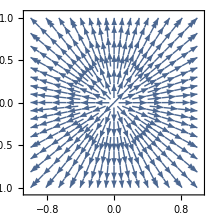

-Graphics3D-

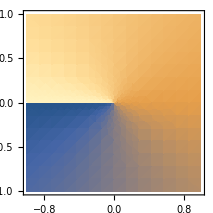

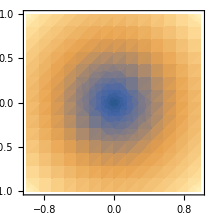

-Graphics3D-

-Graphics3D-

```mathematica
f[x_,y_]:=x+ⅈ y;
f[x,y]
StreamPlot[{Re[f[x,y]], Im[f[x,y]]}, {x,-1,1}, {y,-1,1}]
Plot3D[{Abs[f[x,y]], Arg[f[x,y]]}, {x,-1,1}, {y,-1,1}]
DensityPlot[ Arg[f[x,y]], {x,-1,1}, {y,-1,1}]
DensityPlot[{Abs[f[x,y]], Arg[f[x,y]]}, {x,-1,1}, {y,-1,1}]
Plot3D[{Re[f[x,y]], Im[f[x,y]]}, {x,-1,1}, {y,-1,1}]
Plot3D[Re[f[x,y]], {x,-1,1}, {y,-1,1}]
```

ⅇ^(x+ⅈ y)

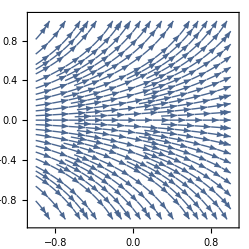

-Graphics3D-

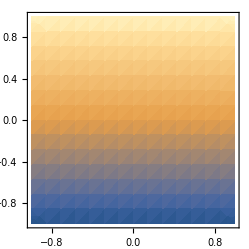

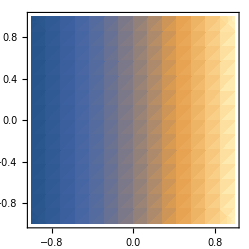

-Graphics3D-

-Graphics3D-

```mathematica
f[x_,y_]:=Exp[x+ⅈ y];
f[x,y]
StreamPlot[{Re[f[x,y]], Im[f[x,y]]}, {x,-1,1}, {y,-1,1}]
Plot3D[{Abs[f[x,y]], Arg[f[x,y]]}, {x,-1,1}, {y,-1,1}]
DensityPlot[ Arg[f[x,y]], {x,-1,1}, {y,-1,1}]
DensityPlot[{Abs[f[x,y]], Arg[f[x,y]]}, {x,-1,1}, {y,-1,1}]
Plot3D[{Re[f[x,y]], Im[f[x,y]]}, {x,-1,1}, {y,-1,1}]
Plot3D[Re[f[x,y]], {x,-1,1}, {y,-1,1}]
```

ⅇ^(-ⅈ t)

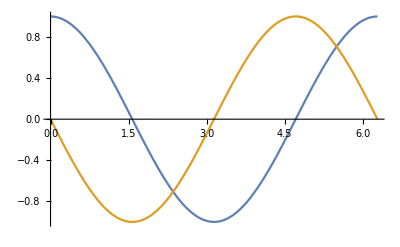

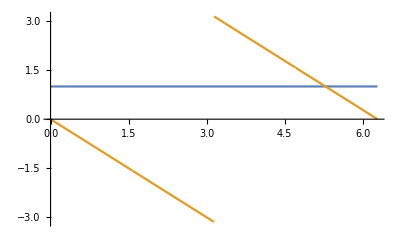

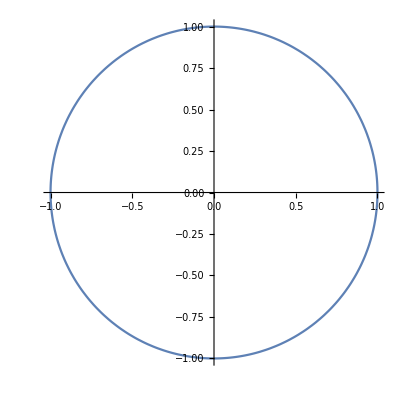

ComplexPlot::plld: Corners for t in {t,1-ⅈ,1+ⅈ} must have distinct machine-precision real and imaginary parts.

ComplexPlot[f[t],{t,1-ⅈ,1+ⅈ}]

```mathematica
f[t_]:=Exp[-ⅈ t];
f[t]
Plot[{Re[f[t]], Im[f[t]]}, {t,0,2 Pi}]
Plot[{Abs[f[t]], Arg[f[t]]}, {t,0,2Pi}]
ParametricPlot[{Re[f[t]], Im[f[t]]} , {t,0,2  Pi}]
ComplexPlot[f[t], {t, 1-ⅈ, 1+ⅈ}]
```